```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/Users/ethanspangler/StabilityProject

```mathematica
"/Users/ethanspangler/Desktop/Twitter"
```

/Users/ethanspangler/Desktop/Twitter

```mathematica
Dissentdata=Import["/Users/ethanspangler/Desktop/Twitter/DissentPlotdata.csv","CSV","HeaderLines"->1] // Dataset
```

```mathematica
Clow={{DateObject[{2016,6,13},"Day","Gregorian",-5.],7275},{DateObject[{2016,7,2},"Day","Gregorian",-5.],27701},{DateObject[{2016,7,16},"Day","Gregorian",-5.],3073},{DateObject[{2016,7,23},"Day","Gregorian",-5.],1951},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],3370},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],4209},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],5779},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],6210},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],4501}};
Cmed= {{DateObject[{2016,6,13},"Day","Gregorian",-5.],2775},{DateObject[{2016,7,2},"Day","Gregorian",-5.],9133},{DateObject[{2016,7,16},"Day","Gregorian",-5.],3479},{DateObject[{2016,7,23},"Day","Gregorian",-5.],442},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],1255},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],3162},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],5065},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],4181},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],13856}};
Chigh={{DateObject[{2016,6,13},"Day","Gregorian",-5.],76},{DateObject[{2016,7,2},"Day","Gregorian",-5.],279},{DateObject[{2016,7,16},"Day","Gregorian",-5.],54},{DateObject[{2016,7,23},"Day","Gregorian",-5.],18},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],48},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],138},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],170},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],248},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],666}};
```

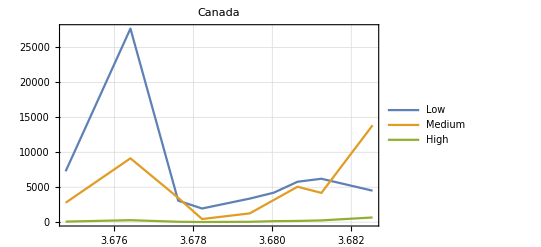

Canada_Dissent.eps

```mathematica
CanadaDissent=DateListPlot[{Clow,Cmed,Chigh},PlotLegends->{"Low","Medium","High"},
PlotRange->Full, 
PlotLabel->"Canada", GridLines->Automatic]
Export["Canada_Dissent.eps",CanadaDissent]
```

```mathematica
Klow={{DateObject[{2016,6,13},"Day","Gregorian",-5.],194},{DateObject[{2016,7,2},"Day","Gregorian",-5.],280},{DateObject[{2016,7,16},"Day","Gregorian",-5.],362},{DateObject[{2016,7,23},"Day","Gregorian",-5.],80},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],30},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],72},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],68},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],116},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],32}};
Kmed= {{DateObject[{2016,6,13},"Day","Gregorian",-5.],13906},{DateObject[{2016,7,2},"Day","Gregorian",-5.],100066},{DateObject[{2016,7,16},"Day","Gregorian",-5.],10644},{DateObject[{2016,7,23},"Day","Gregorian",-5.],7076},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],5842},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],17557},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],6201},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],11132},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],3656}};
Khigh={{DateObject[{2016,6,13},"Day","Gregorian",-5.],157},{DateObject[{2016,7,2},"Day","Gregorian",-5.],513},{DateObject[{2016,7,16},"Day","Gregorian",-5.],106},{DateObject[{2016,7,23},"Day","Gregorian",-5.],30},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],44},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],70},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],18},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],94},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],6}};
```

```mathematica
KenyaDissent= DateListPlot[{Klow,Kmed,Khigh},
PlotLegends->{"Low","Medium","High"},
PlotRange->Full, PlotLabel->"Kenya", GridLines->Automatic];
Export["Kenya_Dissent.eps",KenyaDissent]
```

Kenya_Dissent.eps

```mathematica
Ctotal={{DateObject[{2016,6,13},"Day","Gregorian",-5.],10126},{DateObject[{2016,7,2},"Day","Gregorian",-5.],37113},{DateObject[{2016,7,16},"Day","Gregorian",-5.],6606},{DateObject[{2016,7,23},"Day","Gregorian",-5.],2411},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],4673},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],7509},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],11014},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],10639},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],19023}};
Ktotal= {{DateObject[{2016,6,13},"Day","Gregorian",-5.],14257},{DateObject[{2016,7,2},"Day","Gregorian",-5.],100859},{DateObject[{2016,7,16},"Day","Gregorian",-5.],11112},{DateObject[{2016,7,23},"Day","Gregorian",-5.],7186},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],5916},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],17699},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],6287},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],11342},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],3694}};
```

```mathematica
TotalDissent= DateListPlot[{Ctotal,Ktotal},PlotLegends->{"Canada","Kenya"},
(*ColorFunction->(Blend[{Red,White},{Black,Red,Green},#3]),*)
PlotStyle->{Red,Darker[Green]},
(*{Blend[{Red,White}],Green},*)
PlotRange->Full, 
PlotLabel->"Total Dissent", 
GridLines->Automatic];
Export["Total_Dissent.eps",TotalDissent]
```

Total_Dissent.eps

```mathematica
Cstability={{DateObject[{2016,6,13},"Day","Gregorian",-5.],6211096},{DateObject[{2016,7,2},"Day","Gregorian",-5.],1694650},{DateObject[{2016,7,16},"Day","Gregorian",-5.],9520673},{DateObject[{2016,7,23},"Day","Gregorian",-5.],26086091},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],13458927},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],8375758},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],5710329},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],5911605},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],3306185}};
Kstability= {{DateObject[{2016,6,13},"Day","Gregorian",-5.],279792.3841},{DateObject[{2016,7,2},"Day","Gregorian",-5.],39550.26344},{DateObject[{2016,7,16},"Day","Gregorian",-5.],358981.2833},{DateObject[{2016,7,23},"Day","Gregorian",-5.],555107.1556},
{DateObject[{2016,8,6},"Day","Gregorian",-5.],674273.161},
{DateObject[{2016,8,13},"Day","Gregorian",-5.],225379.9661},
{DateObject[{2016,8,20},"Day","Gregorian",-5.],634483.8588},
{DateObject[{2016,8,27},"Day","Gregorian",-5.],351701.6417},
{DateObject[{2016,9,11},"Day","Gregorian",-5.],1079859.237}};
```

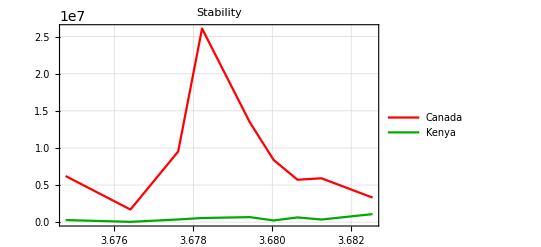

/Users/ethanspangler/StabilityProject/Political_Stability.eps

```mathematica
PoliticalStability=DateListPlot[{Cstability,Kstability},PlotLegends->{"Canada","Kenya"},PlotStyle->{Red,Darker[Green]},PlotRange->Full, PlotLabel->"Stability", GridLines->Automatic]
Export["/Users/ethanspangler/StabilityProject/Political_Stability.eps",PoliticalStability]
```

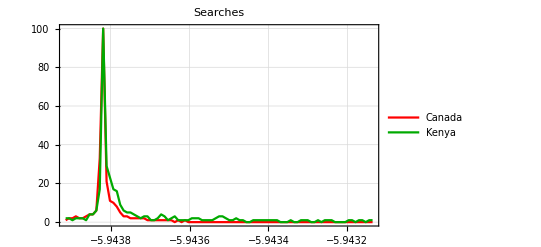

```mathematica
Brexitdata=DeleteCases[Import["/Users/ethanspangler/StabilityProject/brexit.csv","HeaderLines"->1,
"DateStringFormat"->{"Month","Day","Year"}],"",2]/.{}->Sequence[];
Brexit=DateListPlot[{Brexitdata[[All,{1,2}]],Brexitdata[[All,{1,3}]]},Joined->True,
PlotLegends->{"Canada","Kenya"},
PlotStyle->{Red,Darker[Green]},
PlotRange->Full, PlotLabel->"Searches", GridLines->Automatic]
Export["Brexit.eps",Brexit];
```

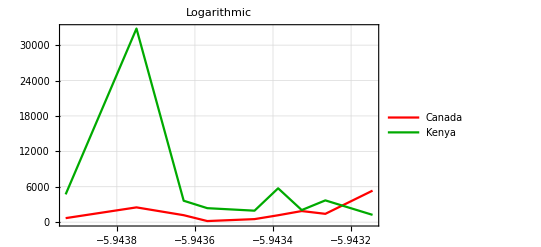

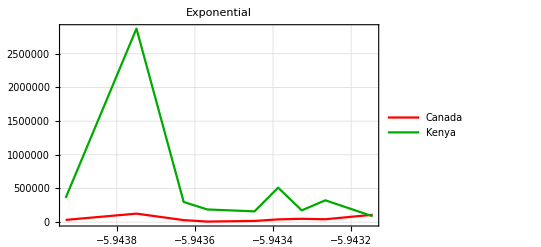

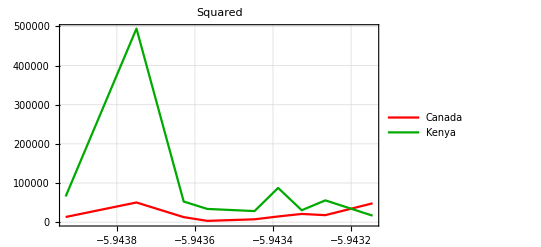

```mathematica
Mono=DeleteCases[Import["/Users/ethanspangler/Desktop/Twitter/MonotonicDissent.csv","HeaderLines"->1,
"DateStringFormat"->{"Month","Day","Year"}],"",2]/.{}->Sequence[];
MonoLog=DateListPlot[{Mono[[All,{1,5}]],Mono[[All,{1,2}]]},Joined->True,
PlotLegends->{"Canada","Kenya"},
PlotStyle->{Red,Darker[Green]},
PlotRange->Full, PlotLabel->"Logarithmic", GridLines->Automatic]
MonoExp=DateListPlot[{Mono[[All,{1,7}]],Mono[[All,{1,4}]]},Joined->True,
PlotLegends->{"Canada","Kenya"},
PlotStyle->{Red,Darker[Green]},
PlotRange->Full, PlotLabel->"Exponential", GridLines->Automatic]
MonoSqr=DateListPlot[{Mono[[All,{1,6}]],Mono[[All,{1,3}]]},Joined->True,
PlotLegends->{"Canada","Kenya"},
PlotStyle->{Red,Darker[Green]},
PlotRange->Full, PlotLabel->"Squared", GridLines->Automatic]
Export["MonoLog.eps",MonoLog];
Export["MonoExp.eps",MonoExp];
Export["MonoSqr.eps",MonoSqr];
```